# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 4 - Variational Method

## 4.2 NONLINEAR VARIATIONAL FUNCTIONS

### 4.2.1 1D particle in a box

```mathematica
psi1DPIB[n_,x_,L_]:=Sqrt[2/L]*Sin[n*Pi*x/L];
energy1DPIB[n_,L_]:=(hbar^2*Pi^2*n^2)/(2*m*L^2);
```

#### No parameters

```mathematica
trial1DPIB[x_,L_]:=x*(L-x);
```

```mathematica
hbar=1;m=1;L=5;(*define parameters for current problem in a.u.*)

variationalGrndState=(*apply variational theorem*)Integrate[trial1DPIB[x,L]*(-(hbar^2/(2*m))*D[trial1DPIB[x,L],{x,2}]),{x,0,L}]/Integrate[(trial1DPIB[x,L])^2,{x,0,L}]
```

1/5

```mathematica
exactGrndState=N[energy1DPIB[1,L]] (*calculate exact n=1, L=5 value*)
```

0.197392

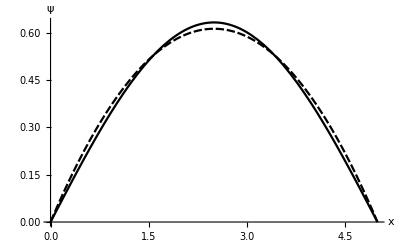

```mathematica
normalizationConst=Sqrt[Integrate[(trial1DPIB[x,L])^2,{x,0,L}]];

Plot[{psi1DPIB[1,x,L],trial1DPIB[x,L]/normalizationConst},
{x,0,L},AxesLabel->{"x","ψ "}]
```

#### With parameters

```mathematica
Clear[a,b,c,d,e,f]
hbar=1;m=1;L=5;
trial1DPIB[x_,a_,b_,c_,d_,e_,f_]:=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;

variationalFunction[x_,a_,b_,c_,d_,e_,f_,L_]:=trial1DPIB[x,a,b,c,d,e,f]/Sqrt[Integrate[(trial1DPIB[xp,a,b,c,d,e,f])^2,{xp,0,L}]];
```

```mathematica
variationalEnergy[a_,b_,c_,d_,e_,f_,L_]:=N[
Integrate[trial1DPIB[x,a,b,c,d,e,f]*(-(hbar^2/(2*m))*D[trial1DPIB[x,a,b,c,d,e,f],{x,2}]),{x,0,L}]/Integrate[(trial1DPIB[x,a,b,c,d,e,f])^2,{x,0,L}]];
```

```mathematica
soln=NMinimize[
{variationalEnergy[a,b,c,d,e,f,L],(*function to minimize*)variationalFunction[0,a,b,c,d,e,f,L]==0,(*constraint 1*)variationalFunction[L,a,b,c,d,e,f,L]==0},(*constraint 2*){{a,-30,30},{b,-30,30},{c,-30,30},(*parameters*)
{d,-30,30},{e,-30,30},{f,-30,30}}]
```

{0.198337,{a→0.0026987,b→-19.7405,c→-8.25987,d→5.86349,e→-0.914502,f→0.0460236}}

```mathematica
(soln[[1]]-N[energy1DPIB[1,L]])/N[energy1DPIB[1,L]]*100
```

0.478479

Erratum: (first printing)  The default NMinimize[] settings in Mathematica 11.1.1.0 find
a slightly lower minimum than the Mathematica 10 version used to produce the manuscript.  Thus the outputs for the remainder of this subsection slightly vary from the version in the first printing.

```mathematica
soln=NMinimize[
{variationalEnergy[a,b,c,d,e,f,L],
variationalFunction[0,a,b,c,d,e,f,L]==0,variationalFunction[L,a,b,c,d,e,f,L]==0},{{a,-10^7,10^-7},{b,22.75,22.76},{c,0.910,0.915},
{d,-2.24,-2.23},{e,0.241,0.242},{f,-0.00250,-0.00245}}]
```

{0.197401,{a→-0.0000120652,b→22.719,c→0.908926,d→-2.2186,e→0.238221,f→-0.00252193}}

```mathematica
(soln[[1]]-N[energy1DPIB[1,L]])/N[energy1DPIB[1,L]]*100
```

0.00469079

```mathematica
soln
```

{0.197401,{a→-0.0000120652,b→22.719,c→0.908926,d→-2.2186,e→0.238221,f→-0.00252193}}

```mathematica
soln[[2]]
```

{a→-0.0000120652,b→22.719,c→0.908926,d→-2.2186,e→0.238221,f→-0.00252193}

```mathematica
soln[[2,1]]
```

a→-0.0000120652

```mathematica
soln[[2,1,2]]
```

-0.0000120652

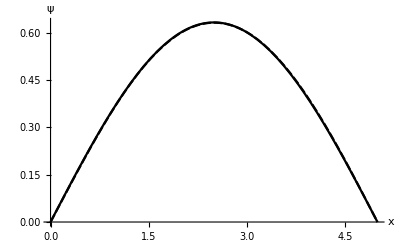

```mathematica
Plot[
{psi1DPIB[1,x,L],
variationalFunction[x,soln[[2,1,2]],soln[[2,2,2]],soln[[2,3,2]],soln[[2,4,2]],soln[[2,5,2]],soln[[2,6,2]],L]},
{x,0,L},AxesLabel->{"x","ψ "}]
```

### 4.2.2 Hydrogen atom

```mathematica
mu=1;(*reduced mass,nearly one*)
el=0;(*orbital angular momentum quantum number*)
Z=1;(*atomic number=number of protons at nucleus=nuclear charge*)

trialHAtom[r_,alpha_]:=Exp[-alpha*r];

variationalEnergy[alpha_]:=4*Pi*NIntegrate[
r^2*trialHAtom[r,alpha]*(-1/(2*mu)*(D[trialHAtom[r,alpha],{r,2}]+(2/r)*D[trialHAtom[r,alpha],{r,1}])+el*(el+1)*trialHAtom[r,alpha]/(2*mu*r^2)-
Z*trialHAtom[r,alpha]/r),{r,10^-6,1000}]/(4*Pi*NIntegrate[r^2*(trialHAtom[r,alpha])^2,{r,10^-6,1000}]);
```

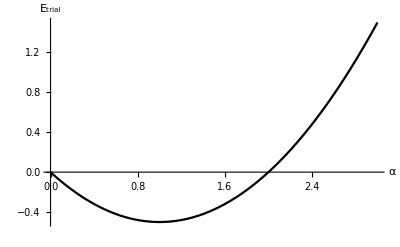

```mathematica
Plot[variationalEnergy[alpha],{alpha,0.0001,3},
AxesLabel->{"α","E_trial"}]
```

```mathematica
NMinimize[variationalEnergy[alpha],{alpha,0.5,1.5}]//Quiet
```

{-0.5,{alpha→1.}}

#### Gaussian orbitals

```mathematica
mu=1;el=0;Z=1;(*set problem parameters,in atomic units*)

trialHAtomGaussian[r_,alpha_]:=(2*alpha/Pi)^(3/4)*Exp[-alpha*r^2];

variationalEnergy[alpha_]:=4*Pi*NIntegrate[
r^2*trialHAtomGaussian[r,alpha]*(-1/(2*mu)*(D[trialHAtomGaussian[r,alpha],{r,2}]+(2/r)*D[trialHAtomGaussian[r,alpha],{r,1}])+el*(el+1)*trialHAtomGaussian[r,alpha]/(2*mu*r^2)-Z*trialHAtomGaussian[r,alpha]/r),{r,10^-6,1000}];

soln=NMinimize[variationalEnergy[alpha],{alpha,0.1,0.5}]//Quiet
```

{-0.423884,{alpha→0.263315}}

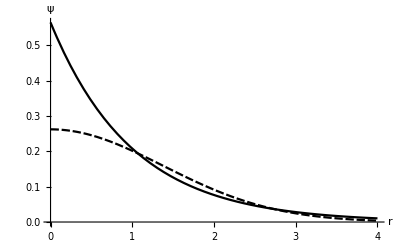

```mathematica
Plot[
{trialHAtom[r,1]/Sqrt[π],trialHAtomGaussian[r,soln[[2,1,2]]]},{r,10^-6,4},AxesLabel->{"r","ψ "}]
```

## 4.3 LINEAR VARIATIONAL FUNCTIONS

### 4.3.2 Orthonormal basis functions: Linear ramp using the particle-in-a-box basis functions

```mathematica
hbar=1;L=5;b=0.1;m=1;(*define constants in a.u.*)
nBasis=2;(*number of basis functions*)

V[x_]:=b*x;

hMatr=Table[N[Integrate[(*calculate each Hamiltonian matrix element*)
psi1DPIB[i,x,L]*(-(1/(2*m))*D[psi1DPIB[j,x,L],{x,2}]+
V[x]*psi1DPIB[j,x,L]),{x,0,L}]],{i,1,nBasis},{j,1,nBasis}];

MatrixForm[hMatr]
```

(0.447392 | -0.0900633
-0.0900633 | 1.03957)

```mathematica
Reverse[Eigenvalues[hMatr]]
```

{0.433997,1.05296}

```mathematica
c=Eigenvectors[hMatr,-1][[1]] (*coefficients of lowest eigenvalue*)
```

{-0.989121,-0.147107}

```mathematica
c.c (*Is the state normalized?*)
```

1.

```mathematica
c.hMatr.c (*energy expectation value*)
```

0.433997

```mathematica
lowestEval[nBasis_]:=Eigenvalues[
Table[N[
Integrate[psi1DPIB[i,x,L]*(-(1/(2*m))*D[psi1DPIB[j,x,L],{x,2}]+V[x]*psi1DPIB[j,x,L]),{x,0,L}]],
{i,1,nBasis},{j,1,nBasis}],-1][[1]];
```

```mathematica
increasingBasis=Table[lowestEval[nBasis],{nBasis,1,10}]
```

{0.447392,0.433997,0.433868,0.433846,0.433845,0.433845,0.433845,0.433845,0.433845,0.433845}

### 4.3.3 Using the linear variational wavefunction

```mathematica
nBasis=5;
hMatr=Table[N[(*build Hamiltonian*)
Integrate[psi1DPIB[i,x,L]*(-(1/(2*m))*D[psi1DPIB[j,x,L],{x,2}]+V[x]*psi1DPIB[j,x,L]),
{x,0,L}]],
{i,1,nBasis},{j,1,nBasis}];

c=Eigenvectors[hMatr,-1][[1]]
```

{0.988862,0.14852,0.00923963,0.00271526,0.000344486}

```mathematica
variationalGroundState[x_]:=Sum[c[[i]]*psi1DPIB[i,x,L],{i,nBasis}]
```

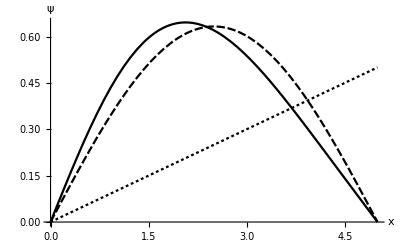

```mathematica
Plot[
{variationalGroundState[x],psi1DPIB[1,x,L],V[x]},
{x,0,L},AxesLabel->{"x","ψ"}]
```

```mathematica
Integrate[variationalGroundState[x]*x*variationalGroundState[x],{x,0,L}]
```

2.23234

```mathematica
xMatr=Table[
Integrate[psi1DPIB[i,x,L]*x*psi1DPIB[j,x,L],{x,0,L}],
{i,nBasis},{j,nBasis}];

MatrixForm[xMatr]
```

(5/2 | -80/(9 π^2) | 0 | -32/(45 π^2) | 0
-80/(9 π^2) | 5/2 | -48/(5 π^2) | 0 | -400/(441 π^2)
0 | -48/(5 π^2) | 5/2 | -480/(49 π^2) | 0
-32/(45 π^2) | 0 | -480/(49 π^2) | 5/2 | -800/(81 π^2)
0 | -400/(441 π^2) | 0 | -800/(81 π^2) | 5/2)

```mathematica
c.xMatr.c
```

2.23234

### 4.3.5 Nonorthonormal basis functions: The 1D particle in a box revisited

```mathematica
hbar=1;L=5;m=1;
basisFn[i_,x_,L_]:=x^i*(L^i-x^i)
MatrixForm[Smatr=Table[
Integrate[basisFn[i,x,L]*basisFn[j,x,L],{x,0,L}],
{i,1,5},{j,1,5}]]
```

(625/6 | 171875/84 | 2734375/72 | 166015625/231 | 30517578125/2184
171875/84 | 3125000/63 | 830078125/792 | 195312500000/9009 | 140380859375/312
2734375/72 | 830078125/792 | 2197265625/91 | 140380859375/264 | 49591064453125/4284
166015625/231 | 195312500000/9009 | 140380859375/264 | 24414062500000/1989 | 110626220703125/399
30517578125/2184 | 140380859375/312 | 49591064453125/4284 | 110626220703125/399 | 11920928955078125/1848)

```mathematica
MatrixForm[
Hmatr=Table[
Integrate[basisFn[i,x,L]*((-1/(2*m))*D[basisFn[j,x,L],{x,2}]),{x,0,L}],{i,1,5},{j,1,5}]]
```

(125/6 | 1250/3 | 234375/28 | 1562500/9 | 244140625/66
1250/3 | 343750/21 | 37109375/84 | 7539062500/693 | 445556640625/1716
234375/28 | 37109375/84 | 615234375/44 | 14892578125/39 | 274658203125/28
1562500/9 | 7539062500/693 | 14892578125/39 | 2587890625000/231 | 804901123046875/2652
244140625/66 | 445556640625/1716 | 274658203125/28 | 804901123046875/2652 | 20503997802734375/2394)

```mathematica
Eigenvalues[{N[Hmatr],N[Smatr]}]
```

{9.06005,3.4726,1.83819,0.79005,0.197394}